Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

__________________________________________________________________________

M 1 : Introduction à Mathematica
__________________________________________________________________________

## Préambule

## I. Introduction (15 min par l’enseignant, et + par l’étudiant...)

### A. Description générale de Mathematica

#### 1. Description générale de Mathematica

Mathematica est un système pour faire des mathématiques avec un ordinateur. Il est développé par Wolfram Research. C’est à la fois :
un logiciel de calcul formel : 
	manipulation d’expressions mathématiques sous forme symbolique, 
	comme le calcul de dérivées, de primitives ou d’intégrales exactes, la simplification d’expressions, etc... 
un logiciel de calcul numérique : 
	évaluation d’expressions mathématiques sous forme numérique (précision machine ou arbitraire),
	comme le calcul des premières décimales du nombre π, évaluation approchée d’intégrales, etc....
un langage de programmation cohérent qui autorise différents paradigmes de programmations : fonctionnelle, par règles, mais aussi procédurale, graphique, etc ...

L’objectif des séances M1 et M2 est précisément de découvrir ce que tout ceci veut dire.

Mathematica est très utilisé dans de très nombreux domaines principalement dans la recherche scientifique, les mathématiques financières, l’enseignement, et dans l’industrie, mais aussi pour la conception de bâtiments, de jeux, ...

#### 2. Où trouver Mathematica ?

L’UPMC a une licence globale permettant d’installer Mathematica sur tous les ordinateurs d’enseignement de l’université, mais aussi sur l’ordinateur personnel des étudiants ou des enseignants. En particulier, il est disponible sur les ordinateurs du L’UTÈS (Bâtiment Atrium), y compris ceux en libre service.

### B. Utiliser Mathematica chez soi

#### 1. Sans installation: Bureau de L’UTÈS

Si vous êtes sous Windows, vous pouvez utiliser Mathematica via une connexion Internet sans rien installer chez vous. Il suffit pour cela d’aller sur le bureau de L’UTÈS : http://lutes.upmc.fr/ts/ 
et suivre les instructions (aide via?) pour ouvrir votre bureau de L’UTÈS à distance.

Une fois sur le bureau de L’UTÈS (Étagère = Compagnon de L’UTÈS), il faut choisir :
	PEDAGOGIE (en haut à droite), 
	puis MATHEMATIQUES, 
	puis plus bas dans la liste dans la rubrique LOGICIELS DE CALCUL on trouve MATHEMATICA.

La connexion à distance est aussi un moyen pour récupérer / travailler sur vos fichiers crées lors des TPs dans les salles de L’UTÈS.
En 2017, la version 11.1.1 de Mathematica est installée à L’UTÈS pour les connections, locales ou à distance, avec authentification, tandis que la version 10 est disponible sans authentification.

#### 2. Avec installation chez vous sur votre ordinateur

Sur le portail Web de l’UPMC ( https://mon.upmc.fr) se trouve dans la rubrique “Mes Outils” l’accès au logiciel Mathematica pour une installation sur n’importe quel ordinateur. L’activation par un mot de passe est liée à l’appartenance à l’UPMC : cette appartenance est vérifiée par votre e-mail (...@etu.upmc.fr) que vous devez donnez lors de votre première inscription sur le site de Wolfram. La version actuelle en téléchargement est la version 11.3.0 qui a quelques fonctionnalités en plus des versions 10.4.1 disponibles à L’UTÈS.

### C. Utiliser Mathematica à L’UTÈS

Pour lancer Mathematica directement dans les salles de L’UTÈS il faut faire comme ci-dessus.

Bannière d’authentification : 
	n° d’étudiant
	mot de passe

Une fois sur le bureau de L’UTÈS (Étagère = Compagnon de L’UTÈS), il faut choisir :
	PEDAGOGIE (en haut à droite), 
	puis MATHEMATIQUES, 
	puis plus bas dans la liste dans la rubrique LOGICIELS DE CALCUL on trouve MATHEMATICA.

Sous Unix, taper dans une fenêtre “Console” : mathematica & et valider.

### D. Organisation

cf. fichier ci-joint PlanTP4M062Txt.pdf

### E. Modes d’évaluation des TP

Fichiers M*Etu.nb rendus sur Moodle

## II. Débuter avec Mathematica (15 min, 0h30)

### A. Interface utilisateur et Noyau

Mathematica est composé de deux parties ou programmes distincts : 
	l’interface avec l’utilisateur ou interface graphique (“Front End”).
	le noyau ("Kernel"). 
Les deux sont reliés par un troisième programme “MathLink” qui gère aussi les liaisons avec les autres langages de programmation.

#### 1. L’interface avec l’utilisateur (“Front End”)

L’interface gère la mise en page et les entrées/sorties. Cette interface de Mathematica est tout à fait remarquable. Elle permet de préparer des entrées de données ou ordres (“inputs”) et d’afficher les sorties (“outputs”) comme expliqués dans la section suivante. Les fichiers créés par Mathematica appelés notebook(s) ou cahiers permettent de résoudre des problèmes interactivement, de saisir les fonctions à exécuter, de faire faire des calculs, et de visualiser les résultats de ces calculs, de générer des graphiques, des sons et des animations, de rédiger.
C’est donc aussi un traitement de texte, qui permet d’inclure du texte parmi les calculs effectués ; ce document a d’ailleurs été rédigé avec Mathematica. 
L’interface dépend de la machine sur laquelle on travaille, mais on retrouve les mêmes grands principes.

#### 2. Le noyau (“Kernel”)

Le noyau constitue le cœur du logiciel; il interprète les instructions d’entrée (écrites en langage Mathematica), puis calcule et retourne le résultat. Il est le même pour tous les ordinateurs PC, Mac, stations UNIX ou LINUX, etc... Il est constitué de milliers de fonctions opérantes en solo ou composées. Ce sont les primitives.

### B. Menu Aide (Help)

Mathematica inclut une documentation exhaustive sous 3 formes principales :
	Recherche par nom : c’est le mode dictionnaire
	Recherche par rubrique : c’est le mode encyclopédique avec un classement hiérarchique par thèmes, puis rubriques, sous-rubriques, ...
	Recherche par guide ou “tutorial” : ce sont environ vingt livres guides rédigés, soit environ 250 Mo.

#### 1. Recherche par nom (mode dictionnaire)

→ Sélectionner un mot proche de celui cherché (en anglais), par exemple plot
   Puis barre de menu  Help⊳ Find Selected Function (ou touche “F1” sous PC, ou “⇑ ⌘ F” sous Mac) 
   Ici la première proposition est la bonne Plot
   en double cliquant sur Plot, on obtient toute la documentation sur la fonction, sa définition, avec des exemples, etc ...

On peut aussi obtenir de l’aide directement dans le notebook en tapant dans une cellule d’Input : ? Plot. 
Mais pour cela il faut solliciter le noyau, ce que nous ferons dans la section III. ci-dessous.

On peut consulter l’aide de l’interface pendant qu’un calcul s’effectue parce que ce sont des programmes distincts.

#### 2. Recherche directe (en mode encyclopédique, i.e. par notions)

Il suffit de rechercher quelque chose (par exemple des fonctions pour faire des tracés de fonctions)
 	soit dans le Help⊳ Documentation Center
	soit dans le Help⊳ Virtual Book 
(Les deux modes ne diffèrent que par leur présentation d’affichage).
On peut alors faire une exploration hiérarchique des fonctions ou recherche par rubrique en double cliquant sur les rubriques d’intérêt.
Solutions :

Help⊳ Documentation Center
Il faut aller ensuite dans VISUALIZATION AND GRAPHICS 
Puis dans 	Function Visualization 		(guide/FunctionVisualization)
où l’on découvre toute la liste de fonctions de tracer : Plot, LogPlot, ...

Help⊳ Virtual Book 
Il faut aller dans VISUALIZATION AND GRAPHICS (dans la fenêtre VIRTUAL BOOK)
Puis dans 	“How to” Topics 		(tutorial/VisualizationAndGraphicsHowToTopicsOverview)
où l’on découvre toute la liste rubriques de possibilités

#### 3. Et aussi : utilisation (éventuelle) des icônes

La fenêtre du DOCUMENTATION CENTER comporte trois icônes en haut à gauche

La “petite maison” est HOME le point de départ dans le documentation center (là où on se trouve) : recherche encyclopédique avec une présentation avec deux niveaux de hiérarchie.

Le F[... ] le FUNCTION NAVIGATOR : recherche encyclopédique.
Similaire au Documentation Center avec plus de deux niveaux de hiérarchie. Il y a quelques différences avec le précédent dans la présentation, et aussi dans le contenu : on y trouve par exemple les add-ons.

Le “livre ouvert” est VIRTUAL BOOK : les livres guides ou “tutorials”

Attention : le système des liens permet de naviguer dans tous les sens !

### C. Notebook = fichier Mathematica = NomDuFichier.nb

Les fichiers Mathematica, sont appelés “notebooks”, et ont pour extension “.nb”.

Les notebooks sont totalement portables (ce sont des fichiers texte ou ASCII). Par exemple, un notebook créé sur un Mac peut être envoyé par courrier électronique, réceptionné, et lu par quelqu’un qui a un PC ou sous Unix, et inversement.

Quelle que soit la plate-forme (PC, Mac, Unix), l’utilisation du fichier est la même à quelques nuances près. 
Ainsi, par exemple sous Mac la touche ⌘ tient lieu (sauf exception) de la touche Ctrl. Sur un Mac on fera le copier/coller en marquant la zone utile puis ⌘ c pour copier et ⌘ v pour coller. Avec un PC, on fera Ctrl c puis Ctrl v et sous Unix, on utilisera (par exemple) le bouton gauche, puis celui du milieu.

Les notebooks Mathematica peuvent contenir des éléments dynamiques comme des animations ou encore des Manipulate. Un notebook peut être exporté en format CDF (Computational Document Format) de Wolfram, un format qui peut être lu par tous grâce à l’installation d’un lecteur gratuit de CDF. On peut donc distribuer ses rapports écrits interactifs Mathematica à des personnes qui n’ont pas de licence Mathematica.

## III. Travailler avec Mathematica (1h30)

Faire cette section en même temps que les exercices de façon progressive.

### A. Dans l’interface seule (45 min avec les exercices)

#### 1. La barre de fenêtre

C’est un outil pratique pour générer des cellules d’un type donné, mais surtout un outil indispensable pour connaître en permanence le type de la cellule dans laquelle on se trouve.

Pour faire apparaître la barre de la fenêtre, il suffit de faire dans la barre de menu :
	 Window ⊳ Toolbar ⊳ Formatting

#### 2. Types utilisés de cellule

L’interface permet de structurer la présentation à l’écran (et le fichier) en cellules (“cells”). Une cellule est constituée d’une ou de plusieurs lignes et est délimitée par un crochet à droite de la fenêtre.

Les cellules sont de différents types. Les types de cellules, les “contenants” que nous utiliserons sont :
	Title
	Subtitle	(ne pas confondre avec Chapter)
	Subsubtitle	(ne pas confondre avec Subchapter)
	Section
	Subsection
	Subsubsection

Ces cellules servent à subdiviser le contenu de la fenêtre, et surtout à le hiérarchiser.

Elles peuvent contenir des cellules “contenues” que nous utiliserons, et notamment :
	Text
	Input
	Output

#### 3. Génération d’une cellule

Pour créer une nouvelle cellule : on observe que le curseur de la souris est vertical quand il passe au dessus d’une cellule, et qu’il est horizontal ailleurs. Dans cette dernière situation, il suffit alors de cliquer dans la fenêtre, vide de cellule, puis de taper sur une touche (une lettre ou la touche ↵ (“retour à la ligne” ou “retour chariot” ou “carriage return”)) pour faire apparaître une nouvelle cellule de type “Input”.

On peut changer le type d’une cellule en sélectionnant le crochet à droite de la cellule, puis en choisissant le type de la cellule dans le menu de la barre de la fenêtre, ou dans le menu : Format ⊳ Style ⊳ Text

On peut aussi créer plus directement une nouvelle cellule d’un type donné à l’aide des raccourcis clavier :
	Mac	PC	Type de cellule générée
	⌘ 1	Alt 1	Title
	⌘ 2	Alt 2	Chapter ou Subtitle (selon les versions et les  styles)
	⌘ 3	Alt 3	Subchapter ou Subsubtitle (idem)
	⌘ 4	Alt 4	Section
	⌘ 5	Alt 5	Subsection
	⌘ 6	Alt 6	Subsubsection	(souvent utilisée)
	⌘ 7	Alt 7	Text		(la plus souvent utilisée)
	⌘ 9	Alt 9	Input		(peu utilisée, car c’est la cellule par défaut)

On rappelle que les cellules “Input” sont créées par défaut.

#### 4. Édition de texte ou d’une cellule

Pour supprimer une cellule, il suffit de la sélectionner (en cliquant sur le crochet qui la délimite), et de la supprimer avec la touche d’effacement (sur Mac) ou la touche suppr (sur PC).

Pour éditer du texte dans une cellule, les opérations habituelles fonctionnent très bien :
	soit en faisant Edit ⊳ Copy		soit en faisant ⌘ c (Mac)	ou	Ctrlc (PC).

Mac	PC	Action
	⌘ x	Ctrlx	couper
	⌘ c	Ctrlc	copier
	⌘ v	Ctrlv	coller
	⌘ z	Ctrlz	revenir en arrière (undo) : une fois seulement dans le texte uniquement

#### 5. Règle d’or d’écriture

Chaque cellule a son style propre, c’est-à-dire une police, une taille de caractère, etc ... Il ne faut jamais (à moins d’avoir de très, très bonnes raisons !) modifier le contenu de la cellule en modifiant ces caractéristiques.

Une raison simple est que l’on peut faire passer le contenu d’une cellule “Text” pour une cellule “Input”, et vice-versa. Bien évidemment on ne sait plus du tout ce que l’on fait.

Mais il y a bien d’autres raisons encore, notamment sur le traitement informatique du notebook par Mathematica. C’est même une source de plantage potentiel pour le système Mathematica qui finit par ne plus savoir que faire !

Au total, il est impératif de se contenter de modifier le type de la cellule !

#### 6. Feuille de style

La feuille de style qui est installé par défaut :
	Format ⪢ Stylesheet ⪢ Default

Il est toujours possible d’adopter un autre style (de cellules) en changeant la feuille de style. 
Le style Standard Report présente l’avantage de mieux distinguer les cellules de type Input/Output et de texte à l’écran. Mais il a l’énorme désavantage d’être coloré : à déconseiller donc.
À moins d’un usage particulier, le style Default est le plus pratique.

Toutefois, pour faire une présentation de type PowerPoint avec des cellules interactives, utiliser par exemple :
	Format ⪢ Stylesheet ⪢ Slideshow ⪢ Earth

Pour créer des Démonstrations avec Mathematica (cf. Aide) :
	 Format ⪢ Stylesheet ⪢ Wolfram ⪢ Demonstration

#### 7. Saisie et édition d’expressions mathématiques : Input ou Text

Plusieurs palettes d’outils sont disponibles dans la barre de menu pour la saisie et l’édition d’expressions mathématiques.

Il est bon de se rappeler que l’on utilise :
(menu Palettes ⪢ Basic Math Assistant) 
					pour saisir et calculer des formules dans une cellule Input 
(menu Palettes ⪢ Writing Assistant)
					pour écrire du texte dans une cellule Text
Et qu’il est préférable de ne pas intervertir : on finit par planter Mathematica.

#### 8. Raccourcis clavier

Pour aller un peu plus vite, il est utile de connaître les raccourcis clavier très utiles (Mac ou PC) dans la suite pour écrire :

les lettres grecques 
- EscaEsc :	α
- EscbEsc :	β et ainsi de suite pour toutes les lettres grecques minuscules
		 γ δ ϵ ζ η θ ι κ λ μ ν ξ ο ω π ρ σ τ υ ϕ χ ψ 
		ou majuscules Δ, Φ, Γ, Λ, Ω, Π, Θ, Σ, Ψ, Ω, et notamment :
- EscpEsc : 	le nombre π 		(équivalent à Pi)

les opérations très courantes : 
- Ctrl 6 : 	puissance 		(exemple : x^2)
- Ctrl 2 : 	racine 			(exemple : √x)
- Ctrl / : 	fraction 		(exemple : 1/2)

les symboles mathématiques usuels : 
- EsceeEsc : 	le nombre d’Euler ⅇ 	(équivalent à E)
- EsciiEsc : 	le nombre imaginaire ⅈ (équivalent à I)
- EscinfEsc : 	l’infini ∞ 		(équivalent à Infinity)
- EscdsNEsc : 	l’ensemble ℕ 		(équivalent à Integers)
- EscdsREsc : 	l’ensemble ℝ 		(équivalent à Reals)

- Esc->Esc :	→ 			(équivalent à une flèche graphique, mais pas à une règle ->)
- EscintEsc :	∫ 			(équivalent à Integrate[])
- EscsumEsc :	∑ 			(équivalent à Sum[])
- EscelEsc :	∈ 			(équivalent à Element[])

etc... pour en connaître d’autres très rapidement il suffit de passer la souris sur le symbole d’intérêt dans la palette Basic Math Assistant ou Writing Assistant.

#### 9. Règle d’écriture

Un paragraphe par cellule.

#### 10. Emboîtement et masquage des cellules

On observe que ces cellules sont hiérarchisées et contiennent par défaut une ou plusieurs cellules en dessous dans la liste.

Ces cellules peuvent être fermées (masquées) ou ouvertes (démasquées) pour ne faire apparaître que les titres ou en-têtes. Pour les ouvrir, double-cliquez dans le crochet (bracket) ou dans le rectangle de la cellule, comme indiqué :

C’est très pratique et très utile pour faciliter la lecture du fichier.

#### 11. Sauvegarde du notebook

Pensez à sauvegarder souvent votre fichier Mathematica (menu File ⊳ Save as, puis "Save" pour les sauvegardes suivantes), les mauvaises manipulations étant fréquentes... Le plus rapide étant ensuite d’utiliser le raccourci clavier : ⌘ s sur le Mac ou Ctrl S sur le PC Windows.

On peut exporter un notebook en entier dans d’autres format comme PDF, CDF ou Teχ via le menu File⊳ Save As. (Ctrl Maj S sous PC ou ⌘ Maj S sous Mac) en choisissant un autre type de ficher dans la liste Type (PC) ou Format (Mac).

On peut par exemple exporter le notebook en PDF en choisissant “PDF Document (*.pdf)”.
Si on veut garder la possibilité de pouvoir interagir avec le document ou garder les éléments dynamiques (animations, Manipulate, ...), il faut choisir “Computable Document (*.cdf)”.

#### 12. Exercices

Vous êtes maintenant équipé pour faire les exercices afférents proposés dans le chapitre “Exercices” ci-dessous.

### B. Dans l’interface avec le noyau (45 min avec les exercices)

#### 1. Faire exécuter un calcul

La touche ↵ permet de générer un saut de ligne dans une cellule, mais pas de faire des calculs comme on s’y attend généralement.

Pour faire un calcul, il faut d’abord 
	générer une cellule de type “Input”,
	écrire 1+1
	valider par ⇧ ↵ ou bien la touche Enter (la touche la plus en bas à droite du pavé numérique)

In[1]:= 1 + 1

Out[1]= 2

Pour évaluer ⇧ ↵ ou la touche Enter. Ne pas confondre avec : aller à la ligne: ↵

#### 2. Indexation des calculs et des résultats

On note que cellule de type “Input” utilisent par défaut des caractères gras de type machine à écrire “courier”. C’est pratiquement le seul type de cellule qui est actif, voire interactif, et qui permet d’effectuer des calculs, tracer des courbes, etc...

Le In[ 1] : = et le Out[ 1] = sont les noms des cellules. Cette numérotation est le moyen que Mathematica utilise pour ranger et cataloguer ses “inputs” et “outputs”. Mathematica conserve la mémoire de tout ce que vous validez par les cellules Input. (Très important pour comprendre le fonctionnement de Mathematica !)
À l’inverse, le noyau de Mathematica ne connaît prend en compte que les cellules qui ont été directement validées, ou les cellules d’Input contenues dans des Sous-sous-sections, Sous-sections, Sections, ... qui ont été globalement validées.

#### 3. L’ordre d’exécution est imposé par l’utilisateur

L’ordre d’exécution est imposé par l’utilisateur (et non par l’ordre du texte)

Il est possible de revenir en arrière dans une cellule, de la modifier, et de la réévaluer. Ce qui compte c’est l’ordre d’évaluation des cellules, pas leur place dans la page, ni l’ordre d’ouverture des notebooks dans lesquels on se trouve.

Une session est la suite des échanges demande-réponse ou Input-Output entre l’utilisateur et le noyau. Demande-réponse c’est le point de vue utilisateur ; Input-Output c’est le point de vue du noyau de Mathematica. Ce qui rentre chez lui et ce qui en ressort. Entre les deux le noyau évalue. Mathematica garde en mémoire toutes les valeurs définies par l’utilisateur pendant une session. Elles s’évanouissent lorsqu’on quitte.

Il est possible de travailler directement avec le noyau sans l’interface. On doit alors se contenter d’un système de calcul avec un éditeur ligne à ligne sommaire.

#### 4. “Running”

Lors du premier calcul, Mathematica initialise la mémoire du noyau, et établit la communication entre le noyau et l’interface. Si l’on observe attentivement, on verra la mention “Running” (sur la barre de titre de la fenêtre), et le doublement de l’épaisseur du crochet de la cellule : ils indiquent que le programme est en cours de calcul.

On peut donc toujours savoir globalement et localement ce que fait le noyau.

#### 5. “Aborting”

La conception de Mathematica sous la forme de plusieurs programmes, essentiellement l’interface “Front End”, et le noyau “Kernel” est très pratique car elle permet notamment d’arrêter un calcul, soit en interrompant le calcul dans le noyau (“Abort” sans quitter le noyau), soit en arrêtant (quittant ou tuant) le noyau (depuis l’interface).

Ainsi si un calcul prend trop de temps et que l’on décide d’y renoncer en cours d’évaluation, il suffit pour cela d’utiliser le menu “Evaluation”, puis “Abort Evaluation”. Si de plus vos instructions sont trop embrouillées, le plus simple est de repartir avec un nouveau noyau en faisant “Evaluation”, puis  “Quit Kernel ”.

Au cours des premières séances de découvertes avec Mathematica, il semble que les débutants aient tendance à saisir des CTRL, ALT, ALT GREC, ESC, ... intempestifs. On dit qu’ils ont les doigts gras (vocabulaire non homologué), car au lieu de saisir une bonne touche simple, ils saisissent par inadvertance des touches composées qui comportent ces touches de contrôles qui ne sont ni imprimables, ni visibles. Par définition, c’est très difficile à mettre en évidence. Par contre Mathematica ne sait pas interpréter ces codes qui ont l’air tout à fait normaux pour nous, mais qui n’ont aucun sens informatique. Rassurez-vous, il semble aussi que ces problèmes disparaissent assez vite au bout d’une séance environ, avec le gain d’un peu d’assurance : il est donc très important de s’entraîner un peu sérieusement à une saisie propre et soigneuse. Avec les caractères de contrôles, vous ne disposez pas d’un clavier, mais d’au moins 5 ou 6 claviers, ce qui requiert une certaine maîtrise.

Pour les raisons évoquées ci-dessus, il peut être (très) utile de quitter, puis de redémarrer le noyau, afin d’effacer de la mémoire tous les résultats des calculs précédents. Pour cela, on utilise le menu “Evaluation” puis “Quit Kernel”. Le noyau sera alors redémarré lors de la validation du prochain calcul.

#### 6. Fonctions Mathematica

Mathematica rassemble un grand nombre de fonctions testées et bien documentées. Toutes les fonctions Mathematica ont un nom généralement explicite NomDeFonction[ ], qui commence par une majuscule avec des arguments mis entre crochets.

Pour taper des crochets [ ] sous Mac, maintenir les touches “ option” et “ shift” enfoncées, et taper “ (“ ou “)”. Sous PC, il faut (souvent) utiliser “alt grec” et taper “ (“ ou “)”.

#### 7. L’essentiel de la syntaxe Mathematica

Les trois éléments essentiels de la syntaxe des expressions :
()	(1+2)		les () servent à regrouper des expressions
[]	Plus[1,2]	Les fonctions Mathematica commencent par une majuscule et l’argument est entre crochets
{}	{1,2,3}		les {} servent à définir les listes (List)

Autres éléments importants de la syntaxe des expressions :
[[ ]]	{a,b,c}[[2]]	Les [[ ]] servent à adresser un élément de la liste, ici le deuxième
“ ”	“A String”	Les “ ” servent à définir les chaînes de caractères
; 	1+1;		supprime les sorties de calcul

#### 8. Saisie d’expressions

On rappelle que la saisie d’expressions mathématiques peut être effectuée avec :
	(menu Palettes ⪢ Basic Math Assistant) 
					pour saisir et calculer des formules dans une cellule Input 
	Des raccourcis clavier peuvent être indiqués dans les cas les plus utilisés.

#### 9. Recherche par nom (mode dictionnaire) dans le noyau

On peut aussi obtenir une aide succincte dans le notebook en tapant dans une cellule d’Input, et en validant avec la touche Enter du pavé numérique, ou bien valider par la combinaison de touches ⇧ ↵ du clavier.

```mathematica
? Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

On observe que Plot[] requiert au moins deux arguments pour fonctionner :
	une fonction (ou une liste de fonctions) de x à tracer
	un domaine de calcul de la fonction, qui sert aussi de domaine de tracer par défaut.

PlotRange est probablement l’une des options les plus importantes de Plot, car elle focalise le tracé sur une région clairement spécifiée du tracé.

La  liste de plus de 100 Options de Plot est obtenue avec Options[Plot], ou aussi en faisant :

```mathematica
?? Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{StyleBox["w", "TI"], "[", SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] plots SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] with features defined by the symbolic wrapper StyleBox["w", "TI"].
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Plot[] est donc une fonction qui demande une certaine attention.

#### 10. Règle d’or d’écriture

Une demande par cellule.

#### 11. Sauvegarde du notebook

Pensez à sauvegarder souvent votre fichier Mathematica. 
Certes, on l’a déjà dit, mais on ne le dit jamais assez.

#### 12. Exercices

Vous êtes maintenant équipé pour faire les exercices afférents proposés dans le chapitre “Exercices” ci-dessous.

## Exercices

À faire avec le fichier joint M1_4M062IntroductionEtu.nb

## I. Interface

### A. Mise en forme

#### → 1. Les cellules et leur hiérarchie

Reproduire avec l’Interface de Mathematica la présentation donnée dans le fichier : M1MiseEnForme1Etu.pdf

### B. Saisie d’expressions

#### → 1. Avec la palette Texte (Writing Assistant)

Dans une cellule “Texte” saisir les formules :

∑_(i=1)^10 i,		∑_(i=1)^n i,	 	(1 | 2
3 | 4)

(NB : utiliser Tab pour passer d’une case à l’autre)

#### → 2. Avec la palette Input (Basic Math Assistant)

Dans une cellule “Input” saisir les formules :

```mathematica
∑_(i=1)^10 i
```

```mathematica
∑_(i=1)^n i
```

#### → 3. Avec la palette et les raccourcis clavier

→ a. Dans une cellule “Texte” saisir les formules :

∑_(i=1)^10 i^2,		∑_(i=1)^n i^2,	 	(α | β
γ | δ)

NB : pour les matrices, on peut aussi utiliser Insert ⊳ Table/Matrix ⊳ New ⊳ ... pour contrôler tous les formats de tables ou de matrices.

→ b. Dans une cellule “Input” saisir la formule :

```mathematica
(x^5+4 x^3+2)Exp[-(y^2)/2]/√Pi
```

sous une forme plus lisible

```mathematica
((x^5+4 x^3+2)ⅇ^(-y^2/2))/(√π)
```

## II. Un tour introductif

Voici quelques calculs que nous soumettons à votre sagacité.
Pour chacune des cellules, nous vous proposons de faire ces démarches successivement :
	1. Bien observer, et Anticiper le résultat attendu : ce qui pourrait / devrait se passer,
	2. Effectuer le calcul dans une fenêtre séparée (un autre notebook vierge) 
		en faisant un copier-coller de la cellule intérieure
	3. Expliquer le résultat du calcul obtenu (LE PLUS IMPORTANT)
	4. Comparer avec la solution cachée et le commentaire en double-cliquant

Cf. la suite du notebook M1IntroductionMMaTxt.nb qui doit être rendu pour que nous puissions suivre votre progression (ce que vous avez compris ou non suivant vos explications).

### A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Bonjour!
```

Bonjour!

Quand Mathematica ne comprend pas, il écrit en bleu et retourne la demande telle quelle.
Il est très important de bien surveiller la couleur interactive des symboles que l’on écrit.

Cette requête est aussi un clin d’oeil au célèbre “Hello World” de Ritchie et Kernighan qu’ils ont utilisé en ouverture de leur livre “C”.

#### 1. Élémentaire

```mathematica
1+1
```

2

Mathematica est capable de faire des calculs sur des entiers comme n’importe quelle calculette.

Si ce résultat est correct, toutes les fonctions de votre Mathematica fonctionnent normalement.

```mathematica
4 a + 5a
```

9 a

```mathematica
4€+5€
```

9 €

On en déduit que Mathematica est un système symbolique. (Infaisable dans un langage procédural, C, ...)
Mathematica sait traiter une expression.
Certes,  a et € sont inconnus puisqu’ils sont en bleu, mais ce sont bien sont des symboles à part entière qui peut être multipliés et additionnés.

On observe aussi que le caractère “blanc” entre 4 et a, qui apparaît automatiquement quand on saisit 4 et a  au clavier, équivaut à la multiplication “*”. On peut le vérifier en faisant :

```mathematica
4 a ==4*a
```

Le symbole == permet de vérifier que les expressions à droite et à gauche sont identiques.

```mathematica
Cos[Pi]
```

-1

Cos[] est une fonction connue de Mathematica et Pi est π un nombre qui a un certain nombre de propriétés connues de Mathematica. On peut le vérifier en faisant :

```mathematica
?Cos
```

```mathematica
?Pi
```

Cos[Pi] a pour argument Pi.
Mathematica connaît les règles de trigonométrie, et en déduit le résultat exact en nombre relatif sans faire de calcul numérique, et sans approximation (ce n’est pas le résultat d’un calcul numérique qui donnerait 1.00000).

```mathematica
Cos[x] /. x -> π
```

-1

Motivation pour cette méthode d’écriture :

Cos[x] est une fonction qui a pour argument x. 
Il est possible d’affecter une valeur à x^(.08), en écrivant x=π. Auquel cas il n’est plus possible de faire de calculs symboliques avec x.
Pour éviter cela, on utilise ici une substitution (/.) et une règle de substitution (x → π) qui affecte ponctuellement une valeur pendant la durée de l’évaluation. C’est la bonne manière de faire.

En règle générale, avec Mathematica, il faut essayer autant que possible d’éviter d’écrire des affectations. En effet, ces affectations rendent inutilisables les symboles, comme dans l’exemple suivant :

```mathematica
(* L'opération suivante calcule la dérivée de x^2 par rapport à x *)
D[x^2,x]
```

2 x

```mathematica
(* Si le symbole x prend la valeur x, alors la dérivation n'est plus possible *)
x=5
D[x^2,x]
```

5

General::ivar: 5 is not a valid variable.

∂_5 25

```mathematica
(* On peut effacer le contenu de x *)
Clear[x]
D[x^2,x]
```

2 x

En programmation procédurale, les dépassements de tableaux sont l’une des premières cause de bogue. En principe, cette source d’erreur ne devrait pas (beaucoup) exister dans Mathematica.
En programmation fonctionnelle, les affectations intempestives sont l’une des premières cause de bogue.

C’est une bogue difficile à repérer pour les enseignants, surtout si vous avez effacé les cellules des affectations, en croyant effacer les affectations : Mathematica se rappelle de tout ce que vous avez transmis au noyau que ce soit, ou que ce ne soit plus dans l’interface, ou dans le fichier notebook.

Expliquer la syntaxe d’écriture avec :
	l’aide disponible de Mathematica de /. ou de -> 
	les notations Infix et notation fonctionnelle standard (voir plus loin)

```mathematica
(Cos[x] /. x -> π)==
ReplaceAll[Cos[x], x -> π]==
ReplaceAll[Cos[x], Rule[x ,π]]
```

True

```mathematica
3x + 2 x
```

5 x

Mathematica est toujours un système symbolique.
x n’a pas été affectée d’une valeur dans le calcul précédent : on peut donc toujours faire un calcul symbolique.

#### 2. Les trois opérations

```mathematica
31 5
315/14
3^100
```

155

45/2

515377520732011331036461129765621272702107522001

Solutions à retenir

On observe aussi que le caractère “espace” entre deux nombres est automatiquement remplacé par une croix est qu’il tient lieu du symbole de multiplication.
On observe que Mathematica effectue normalement l’addition et la multiplication,
	mais qu’il simplifie la division en fraction irréductible par une décomposition en nombres premiers,
	et qu’il a calculé le résultat exact pour 3^100 
		(3 à la puissance 100, le signe ^ signifie “mettre à la puissance”), 
		autrement dit, il a explicitement calculé les 99 multiplications par 3.

#### 3. Valeurs numériques approchées N[]

Il faut donc retenir qu’a priori, Mathematica calcule toujours de façon symbolique et utilise les règles de l’algèbre pour simplifier et obtenir un résultat exact. Mathematica est d’abord un système symbolique, et c’est aussi principalement un langage de programmation fonctionnel.

Pour obtenir une valeur numérique, on peut utiliser la fonction N[ ] qui convertit le calcul sous forme Numérique ordinaire. Cette fonction N[ ], se présente, comme toutes les fonctions Mathematica, sous la forme d’un nom commençant par une majuscule avec des arguments mis entre crochets. Elle est très (très) utilisée, d’où son nom (exceptionnellement) très court.

Pour corriger une erreur ou modifier un calcul dans une cellule, cliquer au point d’intervention et modifier en conséquence, puis validez.

```mathematica
N[315/14]
N[3^100]
N[3^100, 20]
```

22.5

5.15378×10^47

5.1537752073201133104×10^47

Pour obtenir une précision de 20 chiffres, entrer : N[3^100,20]
Noter que la fonction N[3^100,20] comporte 2 arguments : 3^100,20.
Mais elle peut être utilisée plus simplement avec un seul argument 3^100. En effet cette fonction affiche par défaut une précision de 6 ou 16 de chiffres.
Méthode très pratique : on peut aussi entrer 3^100//N ce qui correspond à envoyer le résultat exact de 3^100 dans le “tuyau” // ou “pipe de la fonction N et l’on obtient toujours 5.15378*10^47. C’est une notation Postfix.

```mathematica
3^100//Timing
3^100;//Timing
```

{0.000012,515377520732011331036461129765621272702107522001}

{5.×10^-6,Null}

Dans ces deux derniers calculs, on affiche le temps de calcul en seconde.
Dans le premier calcul on affiche aussi le résultat, tandis que dans le second, le “;” supprime l’affichage du résultat.

Retenir : l’effet du “;”.

#### 4. Quelques tests utiles à partir de calcul de puissances pour comprendre

Ces types de tests sont très importants pour utiliser Mathematica à bon escient :

```mathematica
3^100;//AbsoluteTiming
3^1000;//AbsoluteTiming
3^10000;//AbsoluteTiming
3^100000;//AbsoluteTiming
3^1000000;//AbsoluteTiming
3^10000000;//AbsoluteTiming
3^100000000;//AbsoluteTiming
3^1000000000;//AbsoluteTiming
```

{0.000034,Null}

{0.000019,Null}

{0.000067,Null}

{0.000961,Null}

{0.012663,Null}

{0.158355,Null}

{2.02099,Null}

General::ovfl: Overflow occurred in computation.

{0.000479,Null}

{0.000036,2.964600951548×10^47712125}

Les temps de calcul sont affichés en seconde. 0.000034 correspond donc à 34 microsecondes. l est nécessaire de ne pas tenter d’afficher le résultat qui nécessiterait un temps d’affichage inimaginable, d’où l’intérêt du point virgule.
On observe que les premiers temps de calcul ne semblent pas très fiables. C’est assez normal sur un système multiprocesseur, et multitâche. À partir de (3^10000;) les temps de calcul sont plus importants et ne sont plus dans la marge d’incertitude. Ils croissent assez régulièrement en fonction de la puissance demandée : grosso modo environ 10 fois plus long pour chaque puissance de 10 supplémentaire. 
Le calcul dépasse les capacités de calcul de l’ordinateur, et spécifiquement probablement la mémoire totale accessible pour le calcul, ici à partir de 3^1000000000;.
IL EST DONC TRÈS IMPORTANT DE SE REPRÉSENTER À CHAQUE INSTANT CE QUE L’ON DEMANDE RÉELLEMENT À MATHEMATICA. Retenir qu’a priori, il calcule symboliquement ou en nombres entiers avec une précision arbitraire.

```mathematica
3.^100000000//AbsoluteTiming
```

{0.001013,2.964600951548×10^47712125}

Il est possible de forcer le calcul numérique, en fixant la précision numérique d’un nombre flottant, ici 3..
Le calcul n’est plus une multiplication en nombres entiers de 100000000 de termes. Il devient un simple exercice de conversion en passant par le logarithme d’un nombre réel.

```mathematica
N[3^100000000];//AbsoluteTiming
N[3.^100000000]//AbsoluteTiming
```

{2.05698,Null}

{0.00004,2.964600951548×10^47712125}

On observe donc que le second calcul, qui est simple conversion de puissance en passant par les log, est :
	2.05698/0.000061=51424.6 plus rapide que le calcul exact en nombre entier.
On voit bien ici que la fonction N[] ne fait que convertir le résultat APRÈS le calcul exact en nombre entier.

On rappelle qu’il n’y a que 86400 secondes dans une journée, et qu’un facteur aussi grand que 51424.6 rend un calcul possible ou impossible très facilement !

Conclusions intermédiaires :
Mathematica est un système symbolique qui calcule a priori en nombres entiers avec une précision arbitraire.
On peut contrôler cette précision en utilisant des nombres flottants, ou décimaux (et non N[]).
On peut contrôler l’affichage avec N[] qui garantit aussi la précision du calcul effectué en n’affichant jamais plus que la précision du calcul.

#### 5. Exemples récapitulatifs

```mathematica
N [π]
```

3.14159

```mathematica
π //N
```

3.14159

```mathematica
N[π,30]
```

3.14159265358979323846264338328

```mathematica
N[π,2000]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989380952572010654858632788659361533818279682303019520353018529689957736225994138912497217752834791315155748572424541506959508295331168617278558890750983817546374649393192550604009277016711390098488240128583616035637076601047101819429555961989467678374494482553797747268471040475346462080466842590694912933136770289891521047521620569660240580381501935112533824300355876402474964732639141992726042699227967823547816360093417216412199245863150302861829745557067498385054945885869269956909272107975093029553211653449872027559602364806654991198818347977535663698074265425278625518184175746728909777727938000816470600161452491921732172147723501414419735685481613611573525521334757418494684385233239073941433345477624168625189835694855620992192221842725502542568876717904946016534668049886272327917860857843838279679766814541009538837863609506800642251252051173929848960841284886269456042419652850222106611863067442786220391949450471237137869609563643719172874677646575739624138908658326459958133904780275901

Les décimales de π ne sont pas stockées dans la mémoire de Mathematica mais calculées à l’aide d’un algorithme extrêmement performant (Wolfram a même remporté un prix pour la performance).

### B. Opérations de base (numériques)

Les calculs numériques avec Mathematica sont posés et effectués de façon habituelle. Voici un exemple avec une soustraction (-), une multiplication (*) et une division (/) sur des nombres réels (flottants) affectés d’une précision bien définie :

```mathematica
(10.2-3.1)*6.2/2.9
```

On peut aussi faire des calculs avec des nombres complexes, le nombre imaginaire ⅈ étant écrit "I" ici :

```mathematica
(2+3I)*(4-5I)
```

On remarque que “*” sert, comme très souvent en informatique, de signe “multiplier”.
On peut utiliser aussi le caractère “espace” (ou le signe “×” à ne pas confondre avec x, ou le produit vectoriel “×”).

### C. Nombres et Fonctions élémentaires

#### 1. Quelques constantes mathématiques

Mathematica dispose de quelques constantes prédéfinies que l’on peut toujours écrire avec un Nom commençant par une majuscule et des lettres, ou bien un symbole comme expliqué plus haut.

== est une notation de type Infix pour la fonction test d’égalité Equal[] entre deux arguments. Tous les tests d’égalité ci-dessous renvoient True quand ils sont validés.

- le nombre π

```mathematica
Pi ==π
```

- le nombre e

```mathematica
E==ⅇ
```

- le nombre imaginaire i

```mathematica
I== ⅈ
```

- l'infini ∞ :

```mathematica
Infinity==∞
```

#### 2. Quelques fonctions mathématiques

Mathematica dispose de nombreuses fonctions prédéfinies dont le nom suit la règle Nom[] :

- racine carrée : √x

```mathematica
Sqrt[x]==√x
```

- exponentielle, e^x, qui peut être notée dans Mathematica de 5 façons toutes équivalentes :

```mathematica
Exp[x]==E^x==E^x==ⅇ^x==ⅇ^x
```

- logarithme népérien : ln(x)

```mathematica
Log[x]
```

- logarithme en base b : log_b(x) (le plus souvent, b=10)

```mathematica
Log[b,x]
```

- fonctions trigonométriques :

```mathematica
Sin[x]
```

```mathematica
Cos[x]
```

```mathematica
Tan[x]
```

- fonctions trigonométriques inverses :

```mathematica
ArcSin[x]
```

```mathematica
ArcCos[x]
```

```mathematica
ArcTan[x]
```

- valeur absolue : |x|

```mathematica
Abs[x]
```

- factorielle : n !

```mathematica
n! ==Factorial[n]
```

Sélectionnez la fonction Cos[] et tapez sur F1 (sous PC) ou ⌘ F (sous Mac) pour afficher la page d'aide de cette fonction.

Explorez d’autres fonctions avec la rubrique SEE ALSO “ref/ArcCos” (en bas de la page)

Revenez à la page d’aide précédente, et explorez TUTORIALS “tutorial/SomeMathematicalFunctions” qui donne une petite liste des fonctions élémentaires.

Revenez à la page d’aide précédente, et explorez MORE ABOUT puis Elementary Functions, “guide/SomeMathematicalFunctions” qui donne la liste des fonctions élémentaires.

### D. Fonctions

#### 1. Programmation procédurale et fonctionnelle

Le même mot “fonction” est utilisé en programmation procédurale, et en programmation fonctionnelle. Or ce mot n’a pas la même signification, car il est utilisé dans des contextes très différents.

La programmation procédurale ou impérative repose sur le modèle des machines à états comme le modèle de la machine de Turing (1936). On s’intéresse à l’état de la mémoire (centrale et différents registres éventuellement) et aux instructions qui modifient son état par des affectations successives. Les mots clés ici sont “état de la mémoire”, “instructions”, et “affectations successives”. Les procédures, encore appelées routines, ou sous-routines, ou fonctions servent donc à modifier l’état de la mémoire au travers d’étapes à réaliser.

La programmation fonctionnelle repose sur l’évaluation de fonctions mathématiques dans un système formel comme dans le lambda-calcul de Church (1930). Les langages fonctionnels les plus anciens sont Lisp (1958), Scheme (1975), et Common Lisp (1984). Par principe, on ne s’intéresse pas à la mémoire, ni à la notion d’état, et aux affectations. Un programme est donc simplement une application, au sens mathématique.

Chaque mode de programmation a un langage particulier, et des méthodes de travail différentes :
Dans le premier cas (procédural), le programmeur doit déclarer tous les objets dans la mémoire pour les manipuler par l’intermédiaire du compilateur.
Dans le second cas (fonctionnel), tous les objets seront déclarés et indexés automatiquement par le programme en temps utile. Le programmeur doit donc se concentrer principalement sur les opérations de réécriture des expressions. Ce travail sur les symboles est souvent plus intuitif et plus naturel car plus proche d’un langage mathématique.

Remarque (un peu spécialisée) sur le typage des variables et des fonctions :
Bien souvent, en tous cas, au niveau débutant, le programmeur ne déclare pas de variables dans Mathematica, et il pourrait finir par penser qu'il n'y a pas de typage des variables. En réalité, tout est typé, car tout est fonction, et donc tout est encapsulé dans quelque chose. Au niveau le plus bas, i.e. au niveau le plus interne on retrouve les feuilles habituelles : les Integer, Real, Character, String, ...
Dans les programmes plus professionnels, tout est normalement typé pour éviter tout abus de langage.

Beaucoup de langages plus récents sont multiparadigmes : procéduraux, fonctionnels, et orientés objet comme Caml (1987), Python (1990), OCaml (1996).

Mathematica est multiparadigme et l’on peut programmer de façon procédurale ou fonctionnelle, ... selon les besoins. Il n’en demeure pas moins que Mathematica est d’abord un système symbolique et fonctionnel.

#### 2. Mode d’utilisation d’une fonction

En dehors de la notation fonctionnelle standard Nom[argument1, argument2, ...], il y a trois façons d’utiliser ou de noter les fonctions :
		Prefix
		Infix
		Postfix

Exemple : Sqrt[2] est la notation fonctionnelle standard de l’extraction d’une racine carrée. 
Le nom de la fonction “Sqrt” est devant l’argument : Sqrt@2 est la notation dite Prefix

```mathematica
Sqrt[2]==Sqrt@2==Sqrt@(2)==√2
```

Exemple : Plus[2, 3] est la notation fonctionnelle standard de l’addition. Le nom de l’opération ou de la fonction “Plus” est devant les arguments 2, et 3, mis en séquence.

```mathematica
Plus[2, 3]
```

Traditionnellement, on utilise la notation de type Infix pour l’addition “+“ :

```mathematica
Plus[2,3]==2~Plus~3==(2+3)
```

Il est aussi possible de mettre les arguments devant le nom de la fonction en utilisant la notation Postfix avec // :

```mathematica
N[√2]==√2//N
```

```mathematica
2//Sqrt==√2
```

En résumé :	Notation fonctionnelle | fonction f | Sqrt | Plus | Traditionnel
Standard | f[x] | Sqrt[2] | Plus[2,3] |  
Prefix | f@x | Sqrt@2 |   |  √2
Infix | x~f~y |   | 2~Plus~3 | 2+3
PostFix | x//f | 2//Sqrt |   |

#### 3. Composition de fonctions, et écriture avec indentation automatique

C’est le mode le plus simple de programmation fonctionnelle. Exemple :

```mathematica
Exp[Cos[x]]
```

Saisir, et constater que la hiérarchie d’indentation est automatiquement respectée à chaque retour à la ligne :

```mathematica
Plot[
Cos[x],
{x,-2π,2π}
]
```

Écrire des fonctions composées en se servant de l’indentation automatique confère une meilleure écriture et une meilleure lecture.

Mais on peut écrire comme on le souhaite, l’exemple ci-dessous ne nécessite pas d’indentation :

```mathematica
Plot[Cos[x],{x,-2π,2π}]
```

On peut faire autant de compositions que souhaitées :

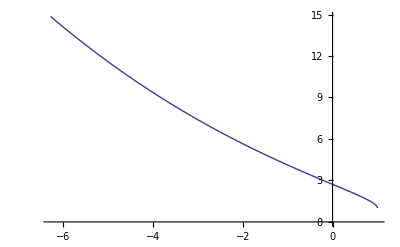

```mathematica
Plot[
Exp[Cos[ArcSin[√x]]],
{x,-2π,1}
]
```

Manipulate[] est utilisé pour faire une animation interactive d’un graphique :

```mathematica
Manipulate[
Plot[
Cos[a x+b],
{x,-2π,2π}
],
{a,1,10},
{b,0,2π}
]
```

a contrôle la fréquence de la fonction sinus, tandis que b contrôle la phase où angle de départ en x=0.

D’une façon générale, on gagne beaucoup de temps à écrire ses fonctions en respectant la hiérarchie de la composition de fonctions. Cela permet généralement de comprendre d’emblée ce qui est fait, et de repérer très rapidement les problèmes d’écriture.

#### 4. Arguments et Options des Fonctions : tracer de courbes

Les fonctions ont généralement des arguments obligatoires, et un certain nombre d’Options que l’on peut ou non rajouter pour préciser la fonction. Étudions la fonction très utile Plot[] au travers des exemples suivants :

Plot comporte deux arguments obligatoires : 
	la fonction à tracer, ⅇ^-x Sin[2 π x]
	et la spécification de l’intervalle sur lequel on cherche à tracer la fonction, {x,0,5}

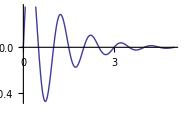

```mathematica
Plot[ⅇ^-x Sin[2 π x],{x,0,5}]
```

On peut rajouter en option AxesLabel→{“Time”,”Ampl.”}, pour spécifier les axes. Elle consiste à remplir avec les contenus donnés dans la liste {“Time”,”Ampl.”} la variable AxesLabel :

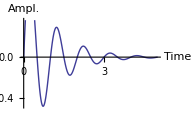

```mathematica
Plot[
ⅇ^-x Sin[2 π x],
{x,0,5},
AxesLabel->{"Time","Ampl."}
]
```

Tracé de plusieurs fonctions sur le même graphe au moyen d’une liste de fonctions à tracer …

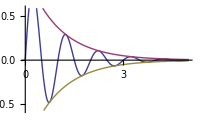

```mathematica
Plot[{ⅇ^-x Sin[2 π x],Exp[-x],-Exp[-x]},{x,0,5}]
```

... de l’utilité des couleurs, et et des labels, et du cadrage de toute la fonction, …

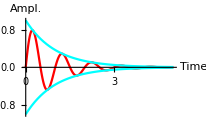

```mathematica
Plot[{
ⅇ^-x Sin[2 π x],
Exp[-x],
-Exp[-x]
},
{x,0,5},
PlotStyle->{RGBColor[1,0,0],Hue[0.5],Hue[0.5]},
AxesLabel->{"Time","Ampl."},
PlotRange->All
]
```

#### 5. Définition de nouvelle fonction par l’utilisateur

Pour définir la fonction f(x)=(a x)/(b+x), il faut écrire la définition ci-dessous, et la valider pour qu’elle soit connue du noyau :

```mathematica
f[x_]:=(a x)/(b+x)
```

On vérifie que f est correctement définie, en interrogeant le noyau :

```mathematica
?f
```

Global`f

f[x_]:=(a x)/(b+x)

Cette fonction est utilisable avec n’importe quel argument, valeur ou expression :
(notez que titi et grosminet sont de couleur bleue car ces variables ne sont pas définies et sont inconnues du système)

```mathematica
f[titi]
```

(a titi)/(b+titi)

```mathematica
f[grosminet]
```

(a grosminet)/(b+grosminet)

```mathematica
f[√5]
```

(√5 a)/(√5+b)

```mathematica
f[y+√2 z+0.3]
```

(a (0.3+y+√2 z))/(0.3+b+y+√2 z)

Nous avons utilisé “:=” qui est le symbole Infix pour une “affectation retardée”. Cela signifie que l’expression toute entière “f[x_]:=(a x)/(b+x)” est mise en mémoire dans le noyau, et chaque fois que l’utilisateur invoquera cette fonction avec un argument quelconque, la fonction sera évaluée comme on l’a vu plus haut. 
On peut donc (très correctement) voir cette expression toute entière comme une règle de remplacement dans un traitement de texte : chaque fois que le noyau rencontrera f[quelqueChose], il remplacera f[quelqueChose] par la partie droite de l’expression (a x)/(b+x).

Il est possible d’utiliser “=” en lieu et place de “:=”. Dans ce cas f[x] prend la valeur de la partie droite de l’expression. On remarque que si x est affectée d’une valeur (x=4), f[x] prend la valeur (4 a)/(b+4)une fois pour toutes. Sauf si l’on recherche spécifiquement ce type de comportement, et en cas de doute, il vaut généralement mieux utiliser “:=”.

Il est possible d’omettre “_” dans “x_”. Dans ce cas f[x] n’est définie que pour x, ce qui n’est généralement pas souhaitable, ni utile.

Une fonction peut avoir plus variables :

```mathematica
g[x_,y_]:=(a x)/(b+x)+(a y^4)/(b+y^4)
```

```mathematica
?g
```

Global`g

g[x_,y_]:=(a x)/(b+x)+(a y^4)/(b+y^4)

Pour que la définition soit générale, i.e. qu’elle s’applique pour n’importe quel nom d’argument, les arguments x, y, ... doivent être des variables muettes, qui ne servent qu’à définir le membre de droite dans l’expression. C’est du tiret bas “_” (souligné ou “underscore” en anglais).

On peut effacer tout ce qui se rattache à la définition de g :

```mathematica
ClearAll[g]
```

```mathematica
?g
```

Global`g

#### 6. Éléments d’étude de fonction

a./ Calcul de la dérivée première de f en utilisant la notation traditionnelle de type Infix :

```mathematica
f'[s]
```

-(a s)/(b+s)^2+a/(b+s)

La notation fonctionnelle de la dérivation de f par rapport à x est :	D[f[x],x] 
On peut facilement calculer la dérivée cinquième ... (cf. documentation dictionnaire)

```mathematica
D[f[x],{x, 5}]==f'''''[x]
D[f[x],{x, 5}]
```

True

-(120 a x)/(b+x)^6+(120 a)/(b+x)^5

b./ Calcul des asymptotes :

```mathematica
Limit[f[x],x->∞]
```

a

```mathematica
Limit[f[x],x->-b]
```

a DirectedInfinity[-Sign[b]]

c./ Calcul de valeurs particulières :

```mathematica
Limit[f'[x],x->0]
```

a/b

d./ Calcul de valeurs particulières par résolution d’équations :

```mathematica
Solve[f[s]==a/2,s]
```

{{s→b}}

En chimie physique la fonction d’adsorption de Langmuir, ou en biologie la fonction de l’équilibre de fixation de deux molécules en interaction, ou encore en enzymologie la fonction de Michaelis-Menten, sont des fonctions homographiques ou hyperboliques comme la fonction f ci-dessus. Cette fonction est caractérisée par la valeur maximale possible asymptotique, a, obtenue pour des concentrations très grandes, à l’infini. Elle est caractérisée aussi par la valeur de la concentration, x, pour laquelle y=f(x) vaut a/2. Cette concentration remarquable est b comme nous le voyons ici.

e./ Tracé de courbes :

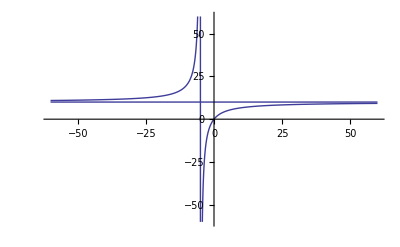

```mathematica
Plot[
{f[x], 10}/.{a->10.0,b->5.0},
{x,-60,60}, 
PlotRange->{-60,60}
]
```

Que remarque-t-on ?

On remarque que Mathematica n’a pas de difficulté avec les singularités..., ici pour x=-b=-5.

En pratique, cette fonction n’est intéressante que pour des valeurs réelles. On résume les résultats dans le graphique :

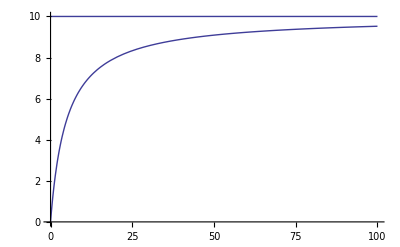

```mathematica
Plot[{f[x], 10}/.{a->10.0,b->5.0},{x,0,100},PlotRange->All]
```

f conserve sa définition symbolique (pas d’effets de bord) :

```mathematica
f[s]
```

(a s)/(b+s)

### E. Graphiques 2D, 3D, sons et animations

#### 1. Représentation graphique

Mathematica permet de représenter facilement n’importe quelle expression sous forme graphique 2D, 3D, 3D animé, et même sous forme sonore. L’un des aspects très pratiques de ces tracés est la possibilité de pouvoir modifier tous les paramètres du graphique très facilement ainsi que l’échelle d’observation. La visualisation permet dans certains cas de comprendre des notions difficiles d’abord. Par exemple avec le tracé suivant, on observe immédiatement que la fonction Sinus[10000/t] présente une curiosité mathématique au voisinage de 0. Pouvez-vous formuler laquelle?

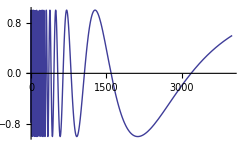

```mathematica
Plot[Sin[10000/t],{t,0,4000}]
```

Mais on arrive toujours à mettre le système en difficulté (Expliquer pourquoi ?):

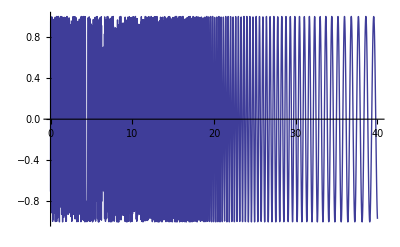

```mathematica
Plot[Sin[10000/t],{t,0,40}]
```

Lorsque Mathematica trace la fonction : il analyse la courbe mathématiquement comme on pourrait le faire pour un problème d’étude de fonction au baccalauréat. Mathematica cherche ensuite à tracer la fonction avec le nombre minimal de points. À droite de la courbe, les oscillations sont bien tracées. Mais ce n’est plus forcément le cas à gauche où les oscillations sont toujours plus resserrées. 
Utiliser Mathematica consiste à s’arranger pour obtenir à ce que l’on cherche sans mettre le système en difficulté.

#### 2. Représentation sonore

On peut d’ailleurs l’écouter, pour ce convaincre de la pathologie de la fonction en ce point. On remarquera que les singularités du type 1/0 ne sont pas un obstacle, ce qui est très appréciable.

```mathematica
Play[Sin[10000/t],{t,-2,-0.001}]
```

-Graphics-

#### 3. Tracé de fonction en 3 dimensions - Animation 3D

Tracé en 3D d’une fonction simple. On trouve ce type de courbe pour décrire la surface d’un cristal.

```mathematica
Plot3D[Sin[x] Sin[y],{x,-5,5},{y,-5,5},PlotPoints->30]
```

-Graphics3D-

```mathematica
Manipulate[
Plot3D[Sin[a x+b] Sin[y],{x,-5,5},{y,-5,5},PlotPoints->30],
{a,1,5},
{b,0,π}
]
```

## I. Suppléments

### A. Langage naturel

Mathematica et Wolfram Alpha (www.wolframalpha.com) peuvent aussi être utilisé en langage naturel, c’est-à-dire à partir de mots anglais. Si on cherche une fonction dont on ne connaît pas très bien le nom, et que l’on ne veut pas recourir à l’aide, on peut :

#### 1. Complétion automatique avec ⌘K

Commencez à saisir le mot, et cherchez tous les mots commençant ainsi :

```mathematica
pl (* puis ⌘K *)
```

```mathematica
Pl (* puis ⌘K *)
```

permet de retrouver le nom de la fonction Plot.

#### 2. = Wolfram Alpha

Saisissez (en anglais) ce que vous cherchez après un signe = placé au tout début de la ligne (Input).
Exemple :

```mathematica
= Plot sinus from 0 to 10
```

Avec un peu de chance Wolfram Alpha comprend votre demande et donne non seulement la solution, mais aussi la traduction de votre demande en syntaxe Mathematica.

Plot sinus from 0 to 10

### B. Step-by-step

Wolfram Alpha Pro (la version payante de Wolfram Alpha) a introduit une nouvelle fonctionnalité, le step-by-step :
	http ://www.wolframalpha.com/pro/step-by-step-math-solver.html
Le step-by-step donne les étapes intermédiaires de la résolution mathématique pour de nombreux problèmes, comme par exemple :
	◃ Résolution d’un système d’équations 
	◃ Calcul d’une dérivée ou d’une primitive 
	◃ Transformations algébriques et trigonométriques (moins évident, à tester)
Ces étapes intermédiaires sont fournies par Wolfram Alpha qui est appelé depuis Mathematica dans un notebook, sans abonnement à la version Pro de Wolfram Alpha. Pour cela on peut faire appel à WolframAlpha avec une petite fonction ShowSteps qui filtre les résultats step-by-step :

```mathematica
ShowSteps[exp_]:=WolframAlpha[ToString@HoldForm@InputForm@exp,TimeConstraint->Infinity,IncludePods->{"Input","Indefinite Integral","Root" ,"Result"},PodStates->{"Step-by-step solution","Show all steps"}]

SetAttributes[ShowSteps,HoldAll]
```

Ceci est une version améliorée de la fonction ShowSteps obtenue sur le site :
	http ://mathematica.stackexchange.com/questions/148/get-a-step-by-step-evaluation- in-mathematica
Il suffit de :
	soit copier-coller cette fonction dans son notebook, puis de l’évaluer, 
	soit l’importer avec :

```mathematica
<< showsteps.m
```

Le fichier showsteps.m est généré automatiquement en validant la totalité du fichier M1showsteps.nb qui est donné sur SAKAI après l’avoir recopié dans le dossier où se trouve ce notebook.

On peut vérifier que la fonction ShowSteps est bien lu dans le noyau avec la commande :

```mathematica
?ShowSteps
```

Puis en la testant avec par exemple :

```mathematica
D[Sin[x^2], x] // ShowSteps
```

## I. Annexes

### A. Wolfram et autour

Voir sur le site dans le répertoire “Livres” :

EIWLStephenWolfram-ElementaryIntroductionWolframLanguage(2015).pdf
	un-langage-pour-ingenieurThierryVerdel2102.pdf

#### 1. Les Add-ons

Des bibliothèques supplémentaires ou Add-ons sont installées dans la distribution de Mathematica et accroissent les potentialités du noyau. Elles ne sont pas normalement chargées dans la mémoire, ni accessibles directement car elles sont habituellement réservées à un usage spécialisé. Pour charger cette bibliothèque de fonctions ou “Package” il faut charger le fichier correspondant comme ceci :

```mathematica
<<StatisticalPlots`
```

Dans le cas présent il sert à utiliser des fonctions de tracés statistiques plus sophistiqués... (hors programme !!!)

#### 2. Wolfram Demonstrations

Wolfram Demo regroupe plus de 10000 démos interactives Mathematica pour expérimenter avec Manipulate une large collection de sujets, et pour mieux comprendre un sujet de mathématique, physique, chimie, biologie, etc...
Elles mettent en valeur les fonctionnalités de Mathematica, même si la création d’une telle démo est hors programme de cette UE.

#### 3. Wolfram Alpha

Wolfram Alpha (www.wolframalpha.com) est un outil en ligne gratuit capable de calculer une réponse à une question (qui doit être posée en anglais). Il utilise une grande base de donnée et Mathematica.
Il permet d’accéder avec un simple navigateur internet à beaucoup des fonctionnalités de Mathematica.
Par exemple, la demande “derivative of sin(x)” (dérivée de sin(x)) calcule la réponse “cos(x)” et donne au passage d’autres informations utiles (propriétés de la fonction, courbes, développements limités, etc...).
À essayer !.

Wolfram Alpha peut être interrogé directement depuis Mathematica avec une connexion Internet.
Dans un nouveau notebook (Ctrl + N) (voir en bas), taper :
== GDP France
Si un message d’erreur apparaît c’est que la connexion Internet n’est pas bien configurée.
Sur les postes de L’UTÈS ou le bureau à distance de L’UTÈS il faut configurer Mathematica pour qu’il puisse accéder à Internet. Dans Mathematica aller dans le menu (sous PC) Edit ⊳ Preferences ou (sous Mac) Mathematica ⊳ Preferences choisir l’onglet Internet Connectivity choisir l’onglet Proxy Setting puis cocher la case Proxy Settings et entrer proxyweb.upmc.fr dans la case HTTP Proxy et 3128 dans la case Port. Tester la connexion Internet avec le button Test Internet Connectivity.

#### 4. Wolfram Education Portal

Sur le Wolfram Education Portal : https://education.wolfram.com/ qui est assez récent, on trouve des cours de math et physique niveau lycée et supérieur. Ces cours sont enrichis avec des applications (“Widgets”) ou démos avec Mathematica. À essayer et surveiller !.
Wolfram a fondé cette initiative pour promouvoir l’apprentissage des maths avec l’ordinateur et Mathematica dès l’école : http://www.computerbasedmath.org/

#### 5. Livres numériques disponibles à l’UPMC

Le point d’entrée pour chercher dans les bibliothèques papier ou numérique est Jubil : “http://www.jubil.upmc.fr”
En haut à droite sur la page d’accueil on peut directement chercher un livre papier ou numérique “Rechercher dans le catalogue”. Alternativement si on cherche uniquement des livres ou revues numériques on peut choisir à gauche “Ressources en ligne>Les livres numériques”, puis la recherche “2. dans la liste A-Z des e-books” est plus adaptée si on connaît déjà le titre.

Hazrat : “Mathematica : A Problem-Centered Approach”. Une introduction à Mathematica avec un point de vue de mathématique autour des nombres.
	
Stan Wagon : “Mathematica in action”. Pour explorer les capacités de Mathematica.

#### 6. Livres imprimés disponibles à l’UPMC

Patrick T. Tam : “A Physicists guide to Mathematica”. Une bonne référence très complète pour les physiciens.

Marvin L. De Jong : “Mathematica for calculus-based physics”. Une introduction courte à Mathematica très accessible est donné dans ce livre, qui présente des calculs numériques de trajectoire de systèmes simples, et plus complexes jusqu’au chaos.

Abell et Braselton : “Mathematica by example”. Un livre un peu ancien, mais avec beaucoup d’exemples et d’exercices.

Jean-Pierre Xémard : “Mathematica théorie et pratique” en 4 tomes (Applications en Arithmétique, Algèbre Analyse, et Géométrie) Une série de livres en français, qui utilise Mathematica de manière approfondie pour faire des maths assez poussées (niveau prépa).

### B. Liens vers d’autres tutoriels/cours à l’UPMC

En Chimie (LC209) : 
http://www.lct.jussieu.fr/pagesperso/toulouse/enseignement/ http://www.lct.jussieu.fr/pagesperso/reinh/enseignement/lc209/enonces.html

En Physique (LP206 et LP207) : http://www.phys.ens.fr/∼jacobsen/LP206/ http://www.lpthe.jussieu.fr/∼zuber/Z_Notes.html

En Biologie (LV204) : 
Disponible à L’UTÈS uniquement : Une fois sur le bureau de L’UTÈS, il faut choisir PEDAGOGIE (en haut à droite), puis BIOLOGIE, puis dans la liste dans la rubrique ENTRAINEMENT ET APPROFONDISSEMENT on trouve LV204. Un double clic sur LV204 produit un dossier LV204 sur votre bureau de L’UTÈS.
 Ce dossier contient les solutions détaillées des TD de Maths de LV204 en format notebook Mathematica ou PDF.

### C. Quelques autres outils et logiciels

Un autre logiciel de calcul formel et numérique très utilisé est Maple. Il a des capacités formelles comparables à celles de Mathematica. Il est également installé sur les ordinateurs du L'UTÈS.

Matlab est un logiciel de calcul numérique très utilisé, mais ne permet pas de faire du calcul formel. C’est la raison pour laquelle Maple et Matlab sont souvent associés. Scilab est un logiciel libre alternatif à Matlab.

Maxima est un des logiciels libres et gratuits qui constituent une alternative aux logiciels commerciaux.

-Graphics-